```mathematica
Clear["Global`*"]
```

```mathematica
exp[t_]:=(a t √(1-(a^2 t^2)/c^2)+c ArcSin[(a t)/c])/(2 a)
```

```mathematica
pos[t_]:=(d-1/2 a t^2)√(1-(a^2 t^2)/c^2)
```

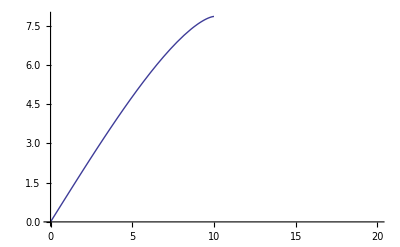

```mathematica
Plot[exp[t]/.{a->0.1,c->1},{t,0,20}]
```